# Pointed Arch Under Uniform Force

Teddy van Jerry

## Calculation of Maximum Normal Stress and Maximum Bending Moment

```mathematica
d=2;
Rep={1,1.2,1.5,1.8,2,3,5,10};
RepResult={};
R[h_]:=d/4+h^2/d;
X[h_]:=(2R[h]-d)/2;
Fr[theta_,R_]:=Abs[(R Cos[theta]-(2R-d)/2)Sin[theta]-(R-(2R-d)/2)/2 √((R-(2R-d)/2)/(R+(2R-d)/2))Cos[theta]];
M[theta_, R_]:=Abs[R(R/2(1-Cos[theta])^2-(R-(2R-d)/2)(1-Cos[theta])-(R-(2R-d)/2)/2 √((R-(2R-d)/2)/(R+(2R-d)/2)))];
Show[Table[Plot[{Fr[x ArcCos[X[i]/R[i]], i],M[x ArcCos[X[i]/R[i]], R[i]]},{x,0,1},PlotRange->All,PlotTheme->"Scientific"],{i,1,2,0.5}]]
StdFr=Maximize[{Fr[theta,R[d/2]], 0<theta<ArcCos[X[d/2]/R[d/2]]},theta][[1]]
StdM=Maximize[{M[theta,R[d/2]], 0<theta<ArcCos[X[d/2]/R[d/2]]},theta][[1]]
Plot[{(Maximize[{Fr[theta,R[h]], 0<theta<ArcCos[X[h]/R[h]]},theta][[1]])/StdFr,(Maximize[{M[theta,R[h]], 0<theta<ArcCos[X[h]/R[h]]},theta][[1]])/StdM},{h, d/2,5d},PlotRange->All,PlotTheme->"Scientific",Filling->Axis]
Plot[{(180/Pi)Limit[theta,Maximize[{Fr[theta,R[h]], 0<theta<ArcCos[X[h]/R[h]]},theta][[2]][[1]]],(180/Pi)Limit[theta,Maximize[{M[theta,R[h]], 0<theta<ArcCos[X[h]/R[h]]},theta][[2]][[1]]]},{h, d/2,5d},PlotRange->All,PlotTheme->"Scientific"]
For[i=1,i≤8,i++,RepResult=Append[RepResult,{i,Rep[[i]],1/StdFr Maximize[{Fr[theta,R[Rep[[i]]]], 0<theta< ArcCos[X[Rep[[i]]]/R[Rep[[i]]]]},theta][[1]],1/StdM Maximize[{M[theta,R[Rep[[i]]]], 0<theta< ArcCos[X[Rep[[i]]]/R[Rep[[i]]]]},theta][[1]]}]]
ExportString[RepResult,"Table"]
Export["D:\\Mathematica files\\Result.xlsx",RepResult];
```

## Calculation Results

## Maximum Values for Three Special Cases

The ratio of height to half width is 1, 1.5 and 2. The outer two lines are 2, the inner two lines are 1 and the middle ones are 1.5.

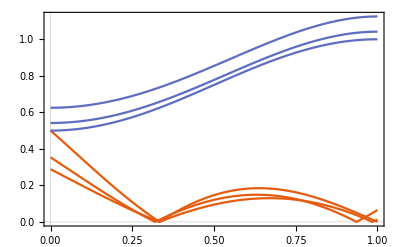

## Special Case - Round Arch

### Maximum Normal Stress

1/2

### Maximum Bending Moment

1

## Maximum Normal Stress and Maximum Bending Moment

The orange line shows the relationship between the ratio of height to half width and maximum normal stress.
The blue line shows the relationship between the ratio of height to half width and maximum bending moment.

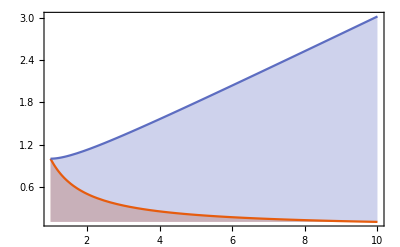

## When Maximum Values are Reached

The x-axis is the ratio of height to half width and the y-axis is the degree when maximum values are reached.
The orange line shows when maximum normal stress is reached. Actually it is reached at the bottom of the arch.
The blue line shows when maximum bending moment is reached. Actually it is reached at the top of the arch.

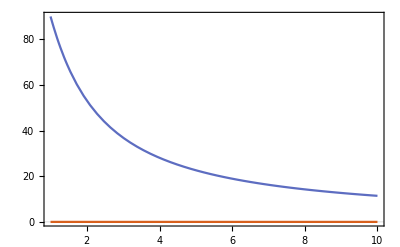

## Table of Values of Some Special Cases

The second column is the ratio of height to half width.
The third column is the maximum normal stress.
The fourth column is the maximum bending moment.
The values are also exported to an Excel file that already exists.

1	1	1	1
2	1.2	0.8333333333333334	1.0083333333333335
3	1.5	0.6666666666666666	1.0416666666666665
4	1.8	0.5555555555555556	1.0888888888888888
5	2	1/2	9/8
6	3	1/3	4/3
7	5	1/5	9/5
8	10	1/10	121/40